```mathematica
Quit[];
```

### Deriving the vev

These are the parameter redefinitions that must be made to properly normalize the meson kinetic term and give the mesons their proper masses:

```mathematica
tildeSubs={fpiT2->fpi^2/(1+(4gG)/9 vs/v),b0TfpiT2->b0 fpi^2/(1+(gf+2/3 gG)vs/v(*+2/27gG(9gf-2gG)vs^2/v^2*))};
```

Scalar potential:

```mathematica
Vs[s_]:=-b0TfpiT2 trM-b0TfpiT2/3(3gf+2gG)s/v trM+1/2 ms^2 s^2
```

```mathematica
(vsTemp==vs/.Solve[(D[Vs[s],s]/.s->vs)==0,vs])/.vsTemp->vs

%/.tildeSubs//Solve[#,vs]&//FullSimplify//StandardForm

Vs[vs]/.tildeSubs/.%;

%⟦1⟧>%⟦2⟧//FullSimplify[#,Assumptions->{v>0,ms>0,b0>0,fpi>0,trM>0,3gf+2gG≠0}]&
```

{vs==(b0TfpiT2 trM (3 gf+2 gG))/(3 ms^2 v)}

{{vs→-(3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms)},{vs→(-3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms)}}

√(4 b0 fpi^2 trM (3 gf+2 gG)^2+9 ms^2 v^2)>0

This demonstrates that this is the scalar’s true vev:

```mathematica
vevSub={vs->(-3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms)};
```

Thankfully it has a well-defined limit when the denominator vanishes:

```mathematica
Limit[(-3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms),gf->-2/3gG,Assumptions->{ms>0,v>0}]
```

0

```mathematica
Series[(-3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms),{ms,∞,4}]//FullSimplify[#,Assumptions->{v>0}]&
```

(b0 fpi^2 trM (3 gf+2 gG))/(3 ms^2 v)-(b0^2 fpi^4 trM^2 (3 gf+2 gG)^3)/(27 ms^4 v^3)+O((1/ms)^5)

```mathematica
FortranForm[(-3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms)]
```

(-3*ms*v + Sqrt(4*b0*fpi**2*(3*gf + 2*gG)**2*trM + 9*ms**2*v**2))/
     -  (6*gf*ms + 4*gG*ms)

### Plotting the vev

```mathematica
subs={trM->2.3+4.8+95.,muq->2.3,mdq->4.8,msq->95.,v->246.*^3,b0->135.^2/(2.3+4.8),fpi->92.2};
```

```mathematica
Solve[Λ==vs/.vevSub/.{gf->1,gG->1},ms]//FullSimplify
%/.subs/.Λ->1000
```

{{ms→-(√5 √b0 fpi √trM)/(√(Λ (5 Λ+3 v)))},{ms→(√5 √b0 fpi √trM)/(√(Λ (5 Λ+3 v)))}}

{{ms→-3.87203},{ms→3.87203}}

```mathematica
vevSub/.{gf->1,gG->1,ms->10}/.subs
```

{vs→150.788}

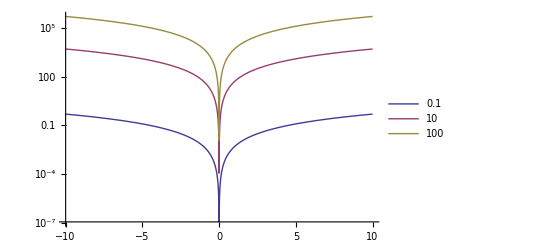

```mathematica
LogPlot[{
Vs[s+vs]-Vs[vs]/.tildeSubs/.vevSub/.{gf->1,gG->1,ms->0.1}/.subs,
Vs[s+vs]-Vs[vs]/.tildeSubs/.vevSub/.{gf->1,gG->1,ms->10}/.subs,
Vs[s+vs]-Vs[vs]/.tildeSubs/.vevSub/.{gf->1,gG->1,ms->100}/.subs
},{s,-10,10},PlotLegends->{0.1, 10, 100}]
```

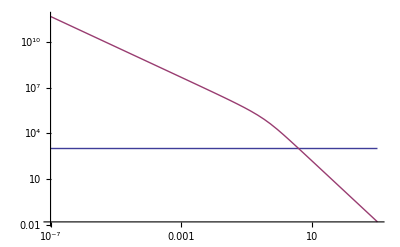

```mathematica
LogLogPlot[{1000,vs/.vevSub/.{gf->1,gG->1,ms->ms}/.subs},{ms,10^-7,1000}]
```

```mathematica
Table[{gf,gG,vs/.vevSub/.{gf->gf,gG->gG,ms->100}/.subs}//N,{gf,10^Range[-7,0,1]},{gG,10^Range[-7,0,1]}];

ListPlot3D[Flatten[%,1],AxesLabel->{"g_f","g_G","v_S (MeV)"},PlotLabel->{"m_S=1 MeV"}]
```

({1.×10^-7,1.×10^-7,0.} | {1.×10^-7,1.×10^-6,0.} | {1.×10^-7,0.00001,7.34047×10^-6} | {1.×10^-7,0.0001,0.0000606313} | {1.×10^-7,0.001,0.000603853} | {1.×10^-7,0.01,0.00603777} | {1.×10^-7,0.1,0.0603769} | {1.×10^-7,1.,0.603768}
{1.×10^-6,1.×10^-7,0.} | {1.×10^-6,1.×10^-6,0.} | {1.×10^-6,0.00001,6.47877×10^-6} | {1.×10^-6,0.0001,0.000061293} | {1.×10^-6,0.001,0.000604676} | {1.×10^-6,0.01,0.00603859} | {1.×10^-6,0.1,0.0603777} | {1.×10^-6,1.,0.603768}
{0.00001,1.×10^-7,9.86832×10^-6} | {0.00001,1.×10^-6,9.31323×10^-6} | {0.00001,0.00001,0.0000149012} | {0.00001,0.0001,0.0000693228} | {0.00001,0.001,0.000612819} | {0.00001,0.01,0.00604674} | {0.00001,0.1,0.0603859} | {0.00001,1.,0.603777}
{0.0001,1.×10^-7,0.0000905883} | {0.0001,1.×10^-6,0.0000912819} | {0.0001,0.00001,0.0000966247} | {0.0001,0.0001,0.000150949} | {0.0001,0.001,0.000694329} | {0.0001,0.01,0.00612825} | {0.0001,0.1,0.0604674} | {0.0001,1.,0.603858}
{0.001,1.×10^-7,0.000905707} | {0.001,1.×10^-6,0.000906256} | {0.001,0.00001,0.000911685} | {0.001,0.0001,0.000966038} | {0.001,0.001,0.00150943} | {0.001,0.01,0.00694334} | {0.001,0.1,0.0612825} | {0.001,1.,0.604673}
{0.01,1.×10^-7,0.00905659} | {0.01,1.×10^-6,0.00905713} | {0.01,0.00001,0.00906256} | {0.01,0.0001,0.0091169} | {0.01,0.001,0.00966029} | {0.01,0.01,0.0150942} | {0.01,0.1,0.0694334} | {0.01,1.,0.612824}
{0.1,1.×10^-7,0.0905653} | {0.1,1.×10^-6,0.0905659} | {0.1,0.00001,0.0905713} | {0.1,0.0001,0.0906256} | {0.1,0.001,0.091169} | {0.1,0.01,0.0966029} | {0.1,0.1,0.150942} | {0.1,1.,0.694332}
{1.,1.×10^-7,0.905649} | {1.,1.×10^-6,0.90565} | {1.,0.00001,0.905655} | {1.,0.0001,0.90571} | {1.,0.001,0.906253} | {1.,0.01,0.911687} | {1.,0.1,0.966025} | {1.,1.,1.50941})

-Graphics3D-

```mathematica
Solve[√(ms^2+p^2)+√(mπ^2+p^2)==mk,p]//FullSimplify
%/.ms->mk-mπ//FullSimplify
```

{{p→-(√((mk-mπ-ms) (mk-mπ+ms) (mk+mπ-ms) (mk+mπ+ms)))/(2 mk)},{p→(√((mk-mπ-ms) (mk-mπ+ms) (mk+mπ-ms) (mk+mπ+ms)))/(2 mk)}}

{{p→0},{p→0}}

```mathematica
√((aa-bb-cc)^2-4 bb cc)/.{aa->493.^2,bb->139.^2,cc->353.^2}
```

13938.9

### Logan’s New Stuff

The Lagrangian containing the Meson kinetic terms, mass terms and interactions with S.

```mathematica
Lag=(fpiT^2/4)mesKIN+(b0T fpiT^2)/2 mesMASS+(fpiT^2 gsGG)/3(S/vh)mesKIN+(b0T fpiT^2)/2(gsff+2gsGG)(S/vh)mesMASS+(b0T fpiT^2)/3(3gsff-2gsGG)gsGG(S^2/vh^2)mesMASS
```

(b0T fpiT^2 gsGG mesMASS S^2 (3 gsff-2 gsGG))/(3 vh^2)+(b0T fpiT^2 mesMASS S (gsff+2 gsGG))/(2 vh)+1/2 b0T fpiT^2 mesMASS+(fpiT^2 gsGG mesKIN S)/(3 vh)+(fpiT^2 mesKIN)/4

Shift the scalar to obtain a vev

```mathematica
Lag2=Lag//ReplaceAll[#,S-> S+vs]&//FullSimplify;
```

Make new replacements for gsGG

```mathematica
Lag3=Lag2//ReplaceAll[#,gsGG->gsGG*vh/(3Lam)]&//FullSimplify;
```

Determine the values of fpiT and b0T in terms of fpi and b0.

```mathematica
fpiTsol=Solve[fpi^2/4==(Lag3//Coefficient[#,mesKIN]&//ReplaceAll[#,S-> 0]&),fpiT]⟦2,1,2⟧//FullSimplify;
```

```mathematica
b0Tsol=Solve[(b0 fpi^2)/2==(Lag3//Coefficient[#,mesMASS]&//ReplaceAll[#,S-> 0]&),b0T]⟦1,1,2⟧//FullSimplify//Series[#,{vs,0,1}]&//Normal//ReplaceAll[#,fpiT-> fpiTsol]&//FullSimplify;
```

Define the scalar potential in terms of v_S. This is done by setting Σ=Σ^†=𝟙 and S=0. Note that we assume that the term in front of S^2 is 1/2 m_S^2. Thus, after setting Σ=Σ^†=𝟙 and S=0, we expand to linear order and add on the correct mass term 1/2 m_S^2.

```mathematica
Pot=-(Series[Lag3//ReplaceAll[#,{mesMASS-> 2 trM,mesKIN-> 0,S-> 0,b0T-> b0Tsol,fpiT-> fpiTsol}]&,{vs,0,1}]//Normal)+1/2 ms^2 vs^2
(*Pot = Pot*)
```

(ms^2 vs^2)/2-b0 fpi^2 trM

Assuming that v_S is small compared to Λ and v_H, we can expand the scalar potential in terms of v_S to quadratic order.

```mathematica
Pot2=Pot
```

(ms^2 vs^2)/2-b0 fpi^2 trM

We now solve for the value of v_S such that (ⅆ V(v_S))/(ⅆ v_S)=0.

```mathematica
vsSol=Solve[D[Pot2,vs]==0,vs]
```

{{vs→0}}

```mathematica
vsSol⟦1,1,2⟧//FortranForm
```

(-36*b0*fpi**4*gsGG*Lam*trM*vh**2)/
     -  (162*b0*fpi**4*gsff**2*Lam**2*trM + 
     -    216*b0*fpi**4*gsff*gsGG*Lam*trM*vh + 
     -    81*fpiT**2*Lam**2*ms**2*vh**2 + 
     -    40*b0*fpi**4*gsGG**2*trM*vh**2)

Below is what you get if you do not assume v_S is small.

```mathematica
vsSol=Solve[D[Pot,vs]==0,vs]//FullSimplify
```

{{vs→((2 2^(1/3) gsGG^2 (b0 fpi^4 trM (3 gsff Lam+2 gsGG vh)^2-9 fpiT^2 Lam^2 ms^2 vh^2)^2)/(((-2 b0^3 trM^3 (3 gsff Lam+2 gsGG vh)^6 fpi^12+54 b0^2 fpiT^2 Lam^2 ms^2 trM^2 vh^2 (3 gsff Lam+2 gsGG vh)^4 fpi^8+729 b0 fpiT^4 Lam^4 ms^4 trM vh^4 (21 gsff^2 Lam^2+28 gsff gsGG vh Lam+4 gsGG^2 vh^2) fpi^4+1458 fpiT^6 Lam^6 ms^6 vh^6) gsGG^3+9 √3 √(b0 fpi^4 fpiT^4 gsGG^6 Lam^4 ms^4 trM vh^4 (9 gsff Lam+2 gsGG vh) (9 gsff Lam+10 gsGG vh) (-4 b0^3 trM^3 (3 gsff Lam+2 gsGG vh)^6 fpi^12+108 b0^2 fpiT^2 Lam^2 ms^2 trM^2 vh^2 (3 gsff Lam+2 gsGG vh)^4 fpi^8+243 b0 fpiT^4 Lam^4 ms^4 trM vh^4 (45 gsff^2 Lam^2+60 gsff gsGG vh Lam+4 gsGG^2 vh^2) fpi^4+2916 fpiT^6 Lam^6 ms^6 vh^6)))^(1/3))-2 gsGG (b0 trM (3 gsff Lam+2 gsGG vh)^2 fpi^4+18 fpiT^2 Lam^2 ms^2 vh^2)+2^(2/3) ((-2 b0^3 trM^3 (3 gsff Lam+2 gsGG vh)^6 fpi^12+54 b0^2 fpiT^2 Lam^2 ms^2 trM^2 vh^2 (3 gsff Lam+2 gsGG vh)^4 fpi^8+729 b0 fpiT^4 Lam^4 ms^4 trM vh^4 (21 gsff^2 Lam^2+28 gsff gsGG vh Lam+4 gsGG^2 vh^2) fpi^4+1458 fpiT^6 Lam^6 ms^6 vh^6) gsGG^3+9 √3 √(b0 fpi^4 fpiT^4 gsGG^6 Lam^4 ms^4 trM vh^4 (9 gsff Lam+2 gsGG vh) (9 gsff Lam+10 gsGG vh) (-4 b0^3 trM^3 (3 gsff Lam+2 gsGG vh)^6 fpi^12+108 b0^2 fpiT^2 Lam^2 ms^2 trM^2 vh^2 (3 gsff Lam+2 gsGG vh)^4 fpi^8+243 b0 fpiT^4 Lam^4 ms^4 trM vh^4 (45 gsff^2 Lam^2+60 gsff gsGG vh Lam+4 gsGG^2 vh^2) fpi^4+2916 fpiT^6 Lam^6 ms^6 vh^6)))^(1/3))/(24 fpiT^2 gsGG^2 Lam ms^2 vh^2)},{vs→(-((16 ⅈ 2^(1/3) (-ⅈ+√3) gsGG^2 (b0 fpi^4 trM (3 gsff Lam+2 gsGG vh)^2-9 fpiT^2 Lam^2 ms^2 vh^2)^2)/(((-2 b0^3 trM^3 (3 gsff Lam+2 gsGG vh)^6 fpi^12+54 b0^2 fpiT^2 Lam^2 ms^2 trM^2 vh^2 (3 gsff Lam+2 gsGG vh)^4 fpi^8+729 b0 fpiT^4 Lam^4 ms^4 trM vh^4 (21 gsff^2 Lam^2+28 gsff gsGG vh Lam+4 gsGG^2 vh^2) fpi^4+1458 fpiT^6 Lam^6 ms^6 vh^6) gsGG^3+9 √3 √(b0 fpi^4 fpiT^4 gsGG^6 Lam^4 ms^4 trM vh^4 (9 gsff Lam+2 gsGG vh) (9 gsff Lam+10 gsGG vh) (-4 b0^3 trM^3 (3 gsff Lam+2 gsGG vh)^6 fpi^12+108 b0^2 fpiT^2 Lam^2 ms^2 trM^2 vh^2 (3 gsff Lam+2 gsGG vh)^4 fpi^8+243 b0 fpiT^4 Lam^4 ms^4 trM vh^4 (45 gsff^2 Lam^2+60 gsff gsGG vh Lam+4 gsGG^2 vh^2) fpi^4+2916 fpiT^6 Lam^6 ms^6 vh^6)))^(1/3)))-32 gsGG (b0 trM (3 gsff Lam+2 gsGG vh)^2 fpi^4+18 fpiT^2 Lam^2 ms^2 vh^2)+8 ⅈ 2^(2/3) (ⅈ+√3) ((-2 b0^3 trM^3 (3 gsff Lam+2 gsGG vh)^6 fpi^12+54 b0^2 fpiT^2 Lam^2 ms^2 trM^2 vh^2 (3 gsff Lam+2 gsGG vh)^4 fpi^8+729 b0 fpiT^4 Lam^4 ms^4 trM vh^4 (21 gsff^2 Lam^2+28 gsff gsGG vh Lam+4 gsGG^2 vh^2) fpi^4+1458 fpiT^6 Lam^6 ms^6 vh^6) gsGG^3+9 √3 √(b0 fpi^4 fpiT^4 gsGG^6 Lam^4 ms^4 trM vh^4 (9 gsff Lam+2 gsGG vh) (9 gsff Lam+10 gsGG vh) (-4 b0^3 trM^3 (3 gsff Lam+2 gsGG vh)^6 fpi^12+108 b0^2 fpiT^2 Lam^2 ms^2 trM^2 vh^2 (3 gsff Lam+2 gsGG vh)^4 fpi^8+243 b0 fpiT^4 Lam^4 ms^4 trM vh^4 (45 gsff^2 Lam^2+60 gsff gsGG vh Lam+4 gsGG^2 vh^2) fpi^4+2916 fpiT^6 Lam^6 ms^6 vh^6)))^(1/3))/(384 fpiT^2 gsGG^2 Lam ms^2 vh^2)},{vs→((16 ⅈ 2^(1/3) (ⅈ+√3) gsGG^2 (b0 fpi^4 trM (3 gsff Lam+2 gsGG vh)^2-9 fpiT^2 Lam^2 ms^2 vh^2)^2)/(((-2 b0^3 trM^3 (3 gsff Lam+2 gsGG vh)^6 fpi^12+54 b0^2 fpiT^2 Lam^2 ms^2 trM^2 vh^2 (3 gsff Lam+2 gsGG vh)^4 fpi^8+729 b0 fpiT^4 Lam^4 ms^4 trM vh^4 (21 gsff^2 Lam^2+28 gsff gsGG vh Lam+4 gsGG^2 vh^2) fpi^4+1458 fpiT^6 Lam^6 ms^6 vh^6) gsGG^3+9 √3 √(b0 fpi^4 fpiT^4 gsGG^6 Lam^4 ms^4 trM vh^4 (9 gsff Lam+2 gsGG vh) (9 gsff Lam+10 gsGG vh) (-4 b0^3 trM^3 (3 gsff Lam+2 gsGG vh)^6 fpi^12+108 b0^2 fpiT^2 Lam^2 ms^2 trM^2 vh^2 (3 gsff Lam+2 gsGG vh)^4 fpi^8+243 b0 fpiT^4 Lam^4 ms^4 trM vh^4 (45 gsff^2 Lam^2+60 gsff gsGG vh Lam+4 gsGG^2 vh^2) fpi^4+2916 fpiT^6 Lam^6 ms^6 vh^6)))^(1/3))-32 gsGG (b0 trM (3 gsff Lam+2 gsGG vh)^2 fpi^4+18 fpiT^2 Lam^2 ms^2 vh^2)-8 2^(2/3) (1+ⅈ √3) ((-2 b0^3 trM^3 (3 gsff Lam+2 gsGG vh)^6 fpi^12+54 b0^2 fpiT^2 Lam^2 ms^2 trM^2 vh^2 (3 gsff Lam+2 gsGG vh)^4 fpi^8+729 b0 fpiT^4 Lam^4 ms^4 trM vh^4 (21 gsff^2 Lam^2+28 gsff gsGG vh Lam+4 gsGG^2 vh^2) fpi^4+1458 fpiT^6 Lam^6 ms^6 vh^6) gsGG^3+9 √3 √(b0 fpi^4 fpiT^4 gsGG^6 Lam^4 ms^4 trM vh^4 (9 gsff Lam+2 gsGG vh) (9 gsff Lam+10 gsGG vh) (-4 b0^3 trM^3 (3 gsff Lam+2 gsGG vh)^6 fpi^12+108 b0^2 fpiT^2 Lam^2 ms^2 trM^2 vh^2 (3 gsff Lam+2 gsGG vh)^4 fpi^8+243 b0 fpiT^4 Lam^4 ms^4 trM vh^4 (45 gsff^2 Lam^2+60 gsff gsGG vh Lam+4 gsGG^2 vh^2) fpi^4+2916 fpiT^6 Lam^6 ms^6 vh^6)))^(1/3))/(384 fpiT^2 gsGG^2 Lam ms^2 vh^2)}}

```mathematica
vsSol
```

```mathematica
vsSol⟦1,1,2⟧//FullSimplify
```

(b0 fpi^4 trM (3 gsff Lam+2 gsGG vh) (3 Lam (vh-gsff vs)-2 gsGG vh vs))/(fpiT^2 Lam ms^2 vh^2 (4 gsGG vs+9 Lam))

```mathematica
oldSol=(-3 ms v+√(4 b0 fpi^2 (3 gf+2 gG)^2 trM+9 ms^2 v^2))/(6 gf ms+4 gG ms);
```